# ITER ECH with Parabolic/toroid Profiles

## Open Additional files:

## Get dispersion routines by evaluating Disper.nb Get plotting and printing routines by evaluating PlotPack.nb Set Parameters by opening a Parameter Window Note: Slab profile models defined in initialization cells at the bottom of this notebook.

## First Do Cold Plasma

### Plot Real and Imaginary parts of nx^2 from 2nd order warm plasma dispersion relation (i.e. E_‖≡0)

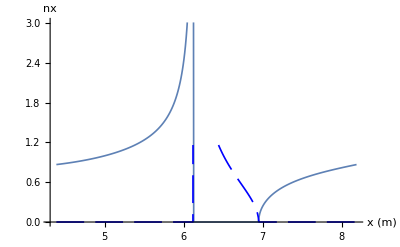

dataSet=S 90HHz

n0=6.24×10^19

b0=5.

freq=170000

rMaj=6.57

rOut=8.19

κ=1.89

ι0=1.2

α1=1.

α2=1.

αT1=1.

αT2=2.

t0=1.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=4.3879

xmax=8.19

```mathematica
nPerpCold[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
     ColdDis0[freq,ne,b,nz,etaList]]
nt=Table[{x,nPerpCold[x]},{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
PPComplexListPlot[nt,"x (m)","nx"]
paramPrint[{dataSet,n0,b0,freq,rMaj,rOut,κ ,ι0,α1,α2,αT1,αT2,t0,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of nx^2 from 4nd order cold plasma dispersion relation (Fast and Slow roots)

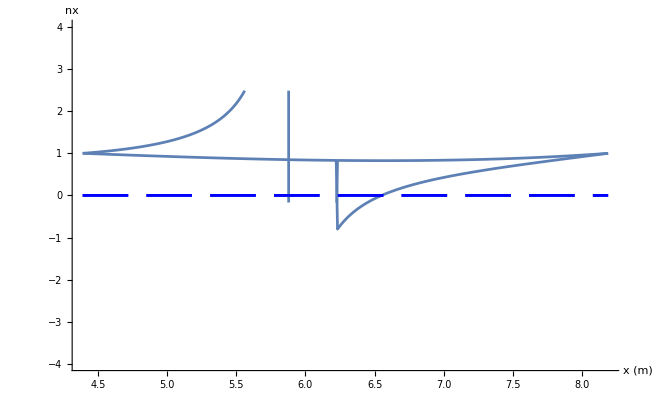

dataSet=Solovev ITER ECH 170GHz

n0=6.24×10^19

b0=5.

freq=170000

rMaj=6.57

rOut=8.19

κ=1.89

ι0=1.2

α1=1.

α2=1.

αT1=1.

αT2=2.

t0=1.

nz=0.01

etaList={0.,1.,0.,0.,0.}

xmin=4.3879

xmax=8.19

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		nxSqColdDisFS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=PPComplexListPlot[nF,"x (m)","nx"];
g2=PPComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-4.,4}]
paramPrint[{dataSet,n0,b0,freq,rMaj,rOut,κ ,ι0,α1,α2,αT1,αT2,t0,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of nx^2 from 4nd order cold plasma dispersion relation (Plus and Minus roots)

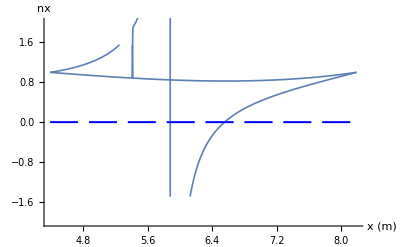

dataSet=Solovev ITER ECH 170GHz

n0=6.24×10^19

b0=5.

freq=170000

rMaj=6.57

rOut=8.19

κ=1.89

ι0=1.2

α1=1.

α2=1.

αT1=1.

αT2=2.

t0=1.

nz=0.01

etaList={0.,1.,0.,0.,0.}

xmin=4.3879

xmax=8.19

```mathematica
nPerp2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		nxSqColdDisPM[freq,ne,b,nz,etaList]]
nt2PM=Table[Flatten[{x,nPerp2PM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦2⟧}];
nM=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦3⟧}];
g1=PPComplexListPlot[nP,"x (m)","nx"];
g2=PPComplexListPlot[nM,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,n0,b0,freq,rMaj,rOut,κ ,ι0,α1,α2,αT1,αT2,t0,nz,etaList,xmin,xmax}];
```

## Now Warm Plasma Stuff

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
(*roots=rootSort[nxwarm];*)
roots=nxwarm;
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList, modelList,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-1.5,1.5}]
ComplexVectorListPlot[rootsRe, "x", "Re[kx]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm, "x", "Re[kx]"]
```

General::munfl: Exp[-3.92768×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.75189×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.8422×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»} cannot be transposed.

Part::partw: Part 2 of Transpose[{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»}] does not exist.

Transpose::nmtx: The first two levels of {{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Re[Transpose[{«1»,{4.39741,0.999343,«4»,-5127.78},«7»,{«1»},«391»}]⟦2⟧]} cannot be transposed.

ListPlot::lpn: Transpose[{{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Re[Transpose[{«1»}]⟦2⟧]}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Im[Transpose[{«1»,{4.39741,0.999343,«4»,-5127.78},«7»,{«1»},«391»}]⟦2⟧]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Im[Transpose[{«1»}]⟦2⟧]}] is not a list of numbers or pairs of numbers.

Part::partw: Part 3 of Transpose[{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Re[Transpose[{«1»}]⟦3⟧]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[«1»,DisplayFunction→Identity].

dataSet=Solovev ITER ECH 170GHz

xProfileMin=xProfileMin

xProfileMax=xProfileMax

nXmin=nXmin

nXmax=nXmax

BXmin=BXmin

BXmax=BXmax

freq=170000

nz=0.01

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=4.3879

xmax=8.19

Show::gtype: Show is not a type of graphics.

Transpose::nmtx: The first two levels of {{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»} cannot be transposed.

Part::partw: Part 2 of Transpose[{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»}] does not exist.

Transpose::nmtx: The first two levels of {{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Re[Transpose[{«1»,{4.39741,0.999343,«4»,-5127.78},«7»,{«1»},«391»}]⟦2⟧]} cannot be transposed.

ListPlot::lpn: Transpose[{{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Re[Transpose[{«1»}]⟦2⟧]}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Im[Transpose[{«1»,{4.39741,0.999343,«4»,-5127.78},«7»,{«1»},«391»}]⟦2⟧]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Im[Transpose[{«1»}]⟦2⟧]}] is not a list of numbers or pairs of numbers.

Part::partw: Part 3 of Transpose[{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{{4.3879,0.99995,0.99995,-0.99995,-0.99995},{4.39741,0.999343,1.00113,5127.78,-0.999343,-1.00113,-5127.78},«8»,«391»},Re[Transpose[{«1»}]⟦3⟧]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{«1»},DisplayFunction→Identity].

Transpose::nmtx: The first two levels of {{4.3879,0,0,0,0},{4.39741,0,0,0,0,0,0},{4.40691,0,0,0,0,0,0},{4.41642,0,0,0,0,0,0},{4.42592,0,0,0,0,0,0},{4.43543,0,0,0,0,0,0},{4.44494,0,0,0,0,0,0},{4.45444,0,0,0,0,0,0},{4.46395,0,0,0,0,0,0},{4.47345,0,0,0,0,0,0},«391»} cannot be transposed.

Part::partw: Part 2 of Transpose[{{4.3879,0,0,0,0},{4.39741,0,0,0,0,0,0},{4.40691,0,0,0,0,0,0},{4.41642,0,0,0,0,0,0},{4.42592,0,0,0,0,0,0},{4.43543,0,0,0,0,0,0},{4.44494,0,0,0,0,0,0},{4.45444,0,0,0,0,0,0},{4.46395,0,0,0,0,0,0},{4.47345,0,0,0,0,0,0},«391»}] does not exist.

Transpose::nmtx: The first two levels of {{{4.3879,0,0,0,0},{4.39741,0,0,0,0,0,0},{4.40691,0,0,0,0,0,0},{4.41642,0,0,0,0,0,0},{4.42592,0,0,0,0,0,0},{4.43543,0,0,0,0,0,0},{4.44494,0,0,0,0,0,0},{4.45444,0,0,0,0,0,0},{4.46395,0,0,0,0,0,0},{4.47345,0,0,0,0,0,0},«391»},Re[Transpose[{«1»}]⟦2⟧]} cannot be transposed.

Transpose::nmtx: The first two levels of {{4.3879,0.,0.,0.,0.},{4.39741,0.,0.,0.,0.,0.,0.},{4.40691,0.,0.,0.,0.,0.,0.},{4.41642,0.,0.,0.,0.,0.,0.},«3»,{4.45444,0.,0.,0.,0.,0.,0.},{4.46395,0.,0.,0.,0.,0.,0.},{4.47345,0.,0.,0.,0.,0.,0.},«391»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{{4.3879,0.,0.,0.,0.},{4.39741,0.,0.,0.,0.,0.,0.},{4.40691,0.,0.,0.,0.,0.,0.},{4.41642,0.,0.,0.,0.,0.,0.},{4.42592,«5»,0.},«1»,{«1»},{4.45444,0.,0.,0.,0.,0.,0.},{4.46395,0.,0.,0.,0.,0.,0.},{4.47345,0.,0.,0.,0.,0.,0.},«391»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{{4.3879,0.,0.,0.,0.},{4.39741,0.,0.,0.,0.,0.,0.},{4.40691,0.,0.,0.,0.,0.,0.},{4.41642,0.,0.,0.,0.,0.,0.},«3»,{4.45444,0.,0.,0.,0.,0.,0.},{4.46395,0.,0.,0.,0.,0.,0.},{4.47345,0.,0.,0.,0.,0.,0.},«391»},Re[Transpose[{«1»}]⟦2⟧]}] is not a list of numbers or pairs of numbers.

ListPlot::lpn: Transpose[{{{4.3879,0.,0.,0.,0.},{4.39741,0.,0.,0.,0.,0.,0.},{4.40691,0.,0.,0.,0.,0.,0.},{4.41642,0.,0.,0.,0.,0.,0.},«3»,{4.45444,0.,0.,0.,0.,0.,0.},{4.46395,0.,0.,0.,0.,0.,0.},{4.47345,0.,0.,0.,0.,0.,0.},«391»},Im[Transpose[{«1»}]⟦2⟧]}] is not a list of numbers or pairs of numbers.

ListPlot::lpn: Transpose[{{{4.3879,0.,0.,0.,0.},{4.39741,0.,0.,0.,0.,0.,0.},{4.40691,0.,0.,0.,0.,0.,0.},{4.41642,0.,0.,0.,0.,0.,0.},«3»,{4.45444,0.,0.,0.,0.,0.,0.},{4.46395,0.,0.,0.,0.,0.,0.},{4.47345,0.,0.,0.,0.,0.,0.},«391»},Re[Transpose[{«1»}]⟦3⟧]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[«1»,DisplayFunction→Identity].

## Now Try with Hot Plasma Dispersion using root finder

```mathematica
nPerpHot[x_,nxGuess_]:=Module[{ne,b,x0,TL,nx0},
		x0=x;
nx0=nxGuess;
     ne=nprof[x0];
b=bprof[x0];
     TL=tprof[x0]*TList;
rootRule=FindRoot[DisFuncGeneral[freq,ne,b,nz,nx,etaList,TL,nminList,nmaxList,modelList],{nx,nx0}, MaxIterations->30];
nx/.rootRule]
```

### First try root finding on warm plasma dispersion rel (model = 1)

```mathematica
modelList =Table[1,{i,1,6}];
```

```mathematica
nxhot[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,nPerpHot[x0,nxGuess]};),{i,1,nPoints}];
nxH];
g7=ComplexVectorListPlot[nxhot[1],"x (m)","nx"];g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g10,g11},PlotRange->All]
Show[{g7,g8,g10,g11},PlotRange->{-.1,.1}]
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

General::munfl: Exp[-157107.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3900.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73688.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

Part::partw: Part 2 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 3 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 4 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$36150} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

General::munfl: Exp[-157107.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3900.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73688.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

Part::partw: Part 2 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 3 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 4 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦6⟧ in search specification {nx,nx0$62064} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$62064,b$62064,nz,nx,etaList,TL$62064,nminList,nmaxList,modelList],{nx,nx0$62064},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$62064,b$62064,nz,nx,etaList,TL$62064,nminList,nmaxList,modelList],{nx,nx0$62064},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$62083,b$62083,nz,nx,etaList,TL$62083,nminList,nmaxList,modelList],{nx,nx0$62083},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$62064,b$62064,nz,nx,etaList,TL$62064,nminList,nmaxList,modelList],{nx,nx0$62064},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$62083,b$62083,nz,nx,etaList,TL$62083,nminList,nmaxList,modelList],{nx,nx0$62083},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$62064,b$62064,nz,nx,etaList,TL$62064,nminList,nmaxList,modelList],{nx,nx0$62064},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$62083,b$62083,nz,nx,etaList,TL$62083,nminList,nmaxList,modelList],{nx,nx0$62083},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

General::munfl: Exp[-157107.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3900.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73688.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

Part::partw: Part 2 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 3 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 4 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦7⟧ in search specification {nx,nx0$67789} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$67789,b$67789,nz,nx,etaList,TL$67789,nminList,nmaxList,modelList],{nx,nx0$67789},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$67789,b$67789,nz,nx,etaList,TL$67789,nminList,nmaxList,modelList],{nx,nx0$67789},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$67808,b$67808,nz,nx,etaList,TL$67808,nminList,nmaxList,modelList],{nx,nx0$67808},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$67789,b$67789,nz,nx,etaList,TL$67789,nminList,nmaxList,modelList],{nx,nx0$67789},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$67808,b$67808,nz,nx,etaList,TL$67808,nminList,nmaxList,modelList],{nx,nx0$67808},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$67789,b$67789,nz,nx,etaList,TL$67789,nminList,nmaxList,modelList],{nx,nx0$67789},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$67808,b$67808,nz,nx,etaList,TL$67808,nminList,nmaxList,modelList],{nx,nx0$67808},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$36150} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$36201} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$36202} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36202,b$36202,nz,nx,etaList,TL$36202,nminList,nmaxList,modelList],{nx,nx0$36202},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$41849,b$41849,nz,nx,etaList,TL$41849,nminList,nmaxList,modelList],{nx,nx0$41849},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882526},«391»},«3»,«15»→Identity].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»],ListPlot[«1»]}},DisplayFunction→Identity].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$36150} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$36201} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$36202} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36202,b$36202,nz,nx,etaList,TL$36202,nminList,nmaxList,modelList],{nx,nx0$36202},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$41849,b$41849,nz,nx,etaList,TL$41849,nminList,nmaxList,modelList],{nx,nx0$41849},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882526},«391»},«3»,«15»→Identity].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»],ListPlot[«1»]}},DisplayFunction→Identity].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$36150} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$36201} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$36202} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36202,b$36202,nz,nx,etaList,TL$36202,nminList,nmaxList,modelList],{nx,nx0$36202},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$41849,b$41849,nz,nx,etaList,TL$41849,nminList,nmaxList,modelList],{nx,nx0$41849},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882526},«391»},«3»,«15»→Identity].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»],ListPlot[«1»]}},DisplayFunction→Identity].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$36150} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$36201} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$36202} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$36202,b$36202,nz,nx,etaList,TL$36202,nminList,nmaxList,modelList],{nx,nx0$36202},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36150,b$36150,nz,nx,etaList,TL$36150,nminList,nmaxList,modelList],{nx,nx0$36150},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$36201,b$36201,nz,nx,etaList,TL$36201,nminList,nmaxList,modelList],{nx,nx0$36201},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$41849,b$41849,nz,nx,etaList,TL$41849,nminList,nmaxList,modelList],{nx,nx0$41849},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882526},«391»},«3»,«15»→Identity].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»],ListPlot[«1»]}},DisplayFunction→Identity].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

dataSet=S 90HHz

ne0=ne0

nsep=nsep

B=B

freq=170000

nz=0.5

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,1,1,1,1}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

#### Now try with hot plasma (model = 2) for all species. Can I find the warm plasma roots with the full dispersion relation?

```mathematica
xPoint=0.;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

Power::infy: Infinite expression 1/0. encountered.

{0.866025,0.866025,-0.866025,-0.866025}

Change model to 2

```mathematica
modelList =Table[2,{i,1,6}];
```

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {0.866025}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {0.866025}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$68632,b$68632,nz,nx,etaList,TL$68632,nminList,nmaxList,modelList],{nx,nx0$68632},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 5 of {0.866025,0.866025,-0.866025,-0.866025} does not exist.

FindRoot::srect: Value {0.866025,0.866025,-0.866025,-0.866025}⟦5⟧ in search specification {nx,nx0$68702} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 6 of {0.866025,0.866025,-0.866025,-0.866025} does not exist.

{nx/.FindRoot[DisFuncGeneral[freq,ne$68632,b$68632,nz,nx,etaList,TL$68632,nminList,nmaxList,modelList],{nx,nx0$68632},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68667,b$68667,nz,nx,etaList,TL$68667,nminList,nmaxList,modelList],{nx,nx0$68667},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68678,b$68678,nz,nx,etaList,TL$68678,nminList,nmaxList,modelList],{nx,nx0$68678},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68689,b$68689,nz,nx,etaList,TL$68689,nminList,nmaxList,modelList],{nx,nx0$68689},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68702,b$68702,nz,nx,etaList,TL$68702,nminList,nmaxList,modelList],{nx,nx0$68702},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68713,b$68713,nz,nx,etaList,TL$68713,nminList,nmaxList,modelList],{nx,nx0$68713},MaxIterations→30]}

dataSet=S 90HHz

ne0=ne0

nsep=nsep

B=B

freq=170000

nz=0.5

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,2,2,2,2}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

Hot plasma root finder gets all roots.  What about at xmin?

```mathematica
xPoint=xmin;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

{0.866025,0.866025,-0.866025,-0.866025}

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {0.866025}.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {0.866025}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {0.866025}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$68740,b$68740,nz,nx,etaList,TL$68740,nminList,nmaxList,modelList],{nx,nx0$68740},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 5 of {0.866025,0.866025,-0.866025,-0.866025} does not exist.

FindRoot::srect: Value {0.866025,0.866025,-0.866025,-0.866025}⟦5⟧ in search specification {nx,nx0$68810} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 6 of {0.866025,0.866025,-0.866025,-0.866025} does not exist.

{nx/.FindRoot[DisFuncGeneral[freq,ne$68740,b$68740,nz,nx,etaList,TL$68740,nminList,nmaxList,modelList],{nx,nx0$68740},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68775,b$68775,nz,nx,etaList,TL$68775,nminList,nmaxList,modelList],{nx,nx0$68775},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68786,b$68786,nz,nx,etaList,TL$68786,nminList,nmaxList,modelList],{nx,nx0$68786},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68797,b$68797,nz,nx,etaList,TL$68797,nminList,nmaxList,modelList],{nx,nx0$68797},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68810,b$68810,nz,nx,etaList,TL$68810,nminList,nmaxList,modelList],{nx,nx0$68810},MaxIterations→30],nx/.FindRoot[DisFuncGeneral[freq,ne$68821,b$68821,nz,nx,etaList,TL$68821,nminList,nmaxList,modelList],{nx,nx0$68821},MaxIterations→30]}

dataSet=S 90HHz

ne0=ne0

nsep=nsep

B=B

freq=170000

nz=0.5

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,2,2,2,2}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

Hot plasma root finder gets 2 of the roots

### Plot hot plasma vs x

```mathematica
g7=ComplexVectorListPlot[nxhot[1],"x (m)","nx"];g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g9,g10,g11,g12},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g7,g8,g9,g10,g11,g12},PlotRange->{-2.,2.},AxesOrigin->{0.,0.}]
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

General::munfl: Exp[-157107.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3900.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73688.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

Part::partw: Part 2 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 3 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 4 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$74084} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

General::munfl: Exp[-157107.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3900.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73688.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

Part::partw: Part 2 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 3 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 4 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦6⟧ in search specification {nx,nx0$99980} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$99980,b$99980,nz,nx,etaList,TL$99980,nminList,nmaxList,modelList],{nx,nx0$99980},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$99980,b$99980,nz,nx,etaList,TL$99980,nminList,nmaxList,modelList],{nx,nx0$99980},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$99999,b$99999,nz,nx,etaList,TL$99999,nminList,nmaxList,modelList],{nx,nx0$99999},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$99980,b$99980,nz,nx,etaList,TL$99980,nminList,nmaxList,modelList],{nx,nx0$99980},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$99999,b$99999,nz,nx,etaList,TL$99999,nminList,nmaxList,modelList],{nx,nx0$99999},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$99980,b$99980,nz,nx,etaList,TL$99980,nminList,nmaxList,modelList],{nx,nx0$99980},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$99999,b$99999,nz,nx,etaList,TL$99999,nminList,nmaxList,modelList],{nx,nx0$99999},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

General::munfl: Exp[-157107.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3900.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73688.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

Part::partw: Part 2 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 3 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 4 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦7⟧ in search specification {nx,nx0$105705} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$105705,b$105705,nz,nx,etaList,TL$105705,nminList,nmaxList,modelList],{nx,nx0$105705},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$105705,b$105705,nz,nx,etaList,TL$105705,nminList,nmaxList,modelList],{nx,nx0$105705},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$105724,b$105724,nz,nx,etaList,TL$105724,nminList,nmaxList,modelList],{nx,nx0$105724},MaxIterations→30]]},«8»,«391»},«3»,«15»→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$105705,b$105705,nz,nx,etaList,TL$105705,nminList,nmaxList,modelList],{nx,nx0$105705},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$105724,b$105724,nz,nx,etaList,TL$105724,nminList,nmaxList,modelList],{nx,nx0$105724},MaxIterations→30]]},«8»,«391»},«3»,«15»→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$105705,b$105705,nz,nx,etaList,TL$105705,nminList,nmaxList,modelList],{nx,nx0$105705},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$105724,b$105724,nz,nx,etaList,TL$105724,nminList,nmaxList,modelList],{nx,nx0$105724},MaxIterations→30]]},«8»,«391»},«3»,«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$74084} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74101} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74102} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74102,b$74102,nz,nx,etaList,TL$74102,nminList,nmaxList,modelList],{nx,nx0$74102},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882525},«391»},«3»,«15»→Identity].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»,PlotJoined→True,AxesLabel→{x (m),nx},PlotStyle→{Thickness[0.003],color,Dashing[{}]},DisplayFunction→Identity],ListPlot[{{4.3879,Im[ReplaceAll[«2»]]},{4.39741,0.},{4.40691,0.},«5»,{4.46395,-1.79773×10^-185},{4.47345,-1.37634×10^-161},«391»},«3»,«15»→Identity]}},«1»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$74084} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74101} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74102} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74102,b$74102,nz,nx,etaList,TL$74102,nminList,nmaxList,modelList],{nx,nx0$74102},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882525},«391»},«3»,«15»→Identity].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»,PlotJoined→True,AxesLabel→{x (m),nx},PlotStyle→{Thickness[0.003],color,Dashing[{}]},DisplayFunction→Identity],ListPlot[{{4.3879,Im[ReplaceAll[«2»]]},{4.39741,0.},{4.40691,0.},«5»,{4.46395,-1.79773×10^-185},{4.47345,-1.37634×10^-161},«391»},«3»,«15»→Identity]}},«1»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$74084} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74101} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74102} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74102,b$74102,nz,nx,etaList,TL$74102,nminList,nmaxList,modelList],{nx,nx0$74102},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882525},«391»},«3»,«15»→Identity].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»,PlotJoined→True,AxesLabel→{x (m),nx},PlotStyle→{Thickness[0.003],color,Dashing[{}]},DisplayFunction→Identity],ListPlot[{{4.3879,Im[ReplaceAll[«2»]]},{4.39741,0.},{4.40691,0.},«5»,{4.46395,-1.79773×10^-185},{4.47345,-1.37634×10^-161},«391»},«3»,«15»→Identity]}},«1»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$74084} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74101} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74102} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74102,b$74102,nz,nx,etaList,TL$74102,nminList,nmaxList,modelList],{nx,nx0$74102},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882525},«391»},«3»,«15»→Identity].

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»,PlotJoined→True,AxesLabel→{x (m),nx},PlotStyle→{Thickness[0.003],color,Dashing[{}]},DisplayFunction→Identity],ListPlot[{{4.3879,Im[ReplaceAll[«2»]]},{4.39741,0.},{4.40691,0.},«5»,{4.46395,-1.79773×10^-185},{4.47345,-1.37634×10^-161},«391»},«3»,«15»→Identity]}},«1»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

dataSet=S 90HHz

ne0=ne0

nsep=nsep

B=B

freq=170000

nz=0.5

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,2,2,2,2}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

```mathematica
Show[{g7,g10},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g8,g11},PlotRange->All,AxesOrigin->{0.,0.}]
Show[{g9,g12},PlotRange->All,AxesOrigin->{0.,0.}]
```

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$74084} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74101} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74102} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74102,b$74102,nz,nx,etaList,TL$74102,nminList,nmaxList,modelList],{nx,nx0$74102},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$94335,b$94335,nz,nx,etaList,TL$94335,nminList,nmaxList,modelList],{nx,nx0$94335},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$94336,b$94336,nz,nx,etaList,TL$94336,nminList,nmaxList,modelList],{nx,nx0$94336},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[«1»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$74084} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74101} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value PlotPack`Private`continue[Transpose[Transpose[]]] in search specification {nx,nx0$74102} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$74102,b$74102,nz,nx,etaList,TL$74102,nminList,nmaxList,modelList],{nx,nx0$74102},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74084,b$74084,nz,nx,etaList,TL$74084,nminList,nmaxList,modelList],{nx,nx0$74084},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$74101,b$74101,nz,nx,etaList,TL$74101,nminList,nmaxList,modelList],{nx,nx0$74101},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$94335,b$94335,nz,nx,etaList,TL$94335,nminList,nmaxList,modelList],{nx,nx0$94335},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$94336,b$94336,nz,nx,etaList,TL$94336,nminList,nmaxList,modelList],{nx,nx0$94336},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[«1»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦3⟧ in search specification {nx,nx0$79777} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$83389,b$83389,nz,nx,etaList,TL$83389,nminList,nmaxList,modelList],{nx,nx0$83389},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882525},«391»},«3»,«15»→Identity].

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦3⟧ in search specification {nx,nx0$79777} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]]},{4.39741,0.},{4.40691,0.},{4.41642,0.},«4»,{4.46395,-1.79773×10^-185},{4.47345,-1.37634×10^-161},«391»},«4»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»,PlotJoined→True,AxesLabel→{x (m),nx},PlotStyle→{Thickness[0.003],color,Dashing[{}]},DisplayFunction→Identity],ListPlot[{{4.3879,Im[ReplaceAll[«2»]]},{4.39741,0.},{4.40691,0.},«5»,{4.46395,-1.79773×10^-185},{4.47345,-1.37634×10^-161},«391»},«3»,«15»→Identity]}},«1»].

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦6⟧ in search specification {nx,nx0$99980} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$99980,b$99980,nz,nx,etaList,TL$99980,nminList,nmaxList,modelList],{nx,nx0$99980},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$99999,b$99999,nz,nx,etaList,TL$99999,nminList,nmaxList,modelList],{nx,nx0$99999},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[«1»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦3⟧ in search specification {nx,nx0$79777} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$83389,b$83389,nz,nx,etaList,TL$83389,nminList,nmaxList,modelList],{nx,nx0$83389},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]]},{4.39741,0.867751},{4.40691,0.869503},«5»,{4.46395,0.880581},{4.47345,0.882525},«391»},«3»,«15»→Identity].

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦3⟧ in search specification {nx,nx0$79777} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$79777,b$79777,nz,nx,etaList,TL$79777,nminList,nmaxList,modelList],{nx,nx0$79777},MaxIterations→30]]},{4.39741,0.},{4.40691,0.},{4.41642,0.},«4»,{4.46395,-1.79773×10^-185},{4.47345,-1.37634×10^-161},«391»},«4»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[«1»,PlotJoined→True,AxesLabel→{x (m),nx},PlotStyle→{Thickness[0.003],color,Dashing[{}]},DisplayFunction→Identity],ListPlot[{{4.3879,Im[ReplaceAll[«2»]]},{4.39741,0.},{4.40691,0.},«5»,{4.46395,-1.79773×10^-185},{4.47345,-1.37634×10^-161},«391»},«3»,«15»→Identity]}},«1»].

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦6⟧ in search specification {nx,nx0$99980} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$99980,b$99980,nz,nx,etaList,TL$99980,nminList,nmaxList,modelList],{nx,nx0$99980},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$99999,b$99999,nz,nx,etaList,TL$99999,nminList,nmaxList,modelList],{nx,nx0$99999},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[«1»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦4⟧ in search specification {nx,nx0$88720} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$88720,b$88720,nz,nx,etaList,TL$88720,nminList,nmaxList,modelList],{nx,nx0$88720},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value {4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38}⟦PlotPack`Private`continue[Transpose[Transpose[]]],2⟧⟦4⟧ in search specification {nx,nx0$88721} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$88721,b$88721,nz,nx,etaList,TL$88721,nminList,nmaxList,modelList],{nx,nx0$88721},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value {4.40691,0.864921,0.869503,2549.8,-0.864921,-0.869503,-2549.8}⟦PlotPack`Private`continue[Transpose[Transpose[]]],3⟧⟦4⟧ in search specification {nx,nx0$88722} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$88722,b$88722,nz,nx,etaList,TL$88722,nminList,nmaxList,modelList],{nx,nx0$88722},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$88720,b$88720,nz,nx,etaList,TL$88720,nminList,nmaxList,modelList],{nx,nx0$88720},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$88721,b$88721,nz,nx,etaList,TL$88721,nminList,nmaxList,modelList],{nx,nx0$88721},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$88720,b$88720,nz,nx,etaList,TL$88720,nminList,nmaxList,modelList],{nx,nx0$88720},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$88721,b$88721,nz,nx,etaList,TL$88721,nminList,nmaxList,modelList],{nx,nx0$88721},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$105705,b$105705,nz,nx,etaList,TL$105705,nminList,nmaxList,modelList],{nx,nx0$105705},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$105724,b$105724,nz,nx,etaList,TL$105724,nminList,nmaxList,modelList],{nx,nx0$105724},MaxIterations→30]]},«8»,«391»},«3»,«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[«1»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦4⟧ in search specification {nx,nx0$88720} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$88720,b$88720,nz,nx,etaList,TL$88720,nminList,nmaxList,modelList],{nx,nx0$88720},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value {4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38}⟦PlotPack`Private`continue[Transpose[Transpose[]]],2⟧⟦4⟧ in search specification {nx,nx0$88721} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$88721,b$88721,nz,nx,etaList,TL$88721,nminList,nmaxList,modelList],{nx,nx0$88721},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value {4.40691,0.864921,0.869503,2549.8,-0.864921,-0.869503,-2549.8}⟦PlotPack`Private`continue[Transpose[Transpose[]]],3⟧⟦4⟧ in search specification {nx,nx0$88722} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$88722,b$88722,nz,nx,etaList,TL$88722,nminList,nmaxList,modelList],{nx,nx0$88722},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$88720,b$88720,nz,nx,etaList,TL$88720,nminList,nmaxList,modelList],{nx,nx0$88720},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$88721,b$88721,nz,nx,etaList,TL$88721,nminList,nmaxList,modelList],{nx,nx0$88721},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$88720,b$88720,nz,nx,etaList,TL$88720,nminList,nmaxList,modelList],{nx,nx0$88720},MaxIterations→30]]},{4.39741,Im[nx/.FindRoot[DisFuncGeneral[freq,ne$88721,b$88721,nz,nx,etaList,TL$88721,nminList,nmaxList,modelList],{nx,nx0$88721},MaxIterations→30]]},«8»,«391»},«3»,DisplayFunction→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

ListPlot::optx: Unknown option PlotJoined in ListPlot[{{4.3879,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$105705,b$105705,nz,nx,etaList,TL$105705,nminList,nmaxList,modelList],{nx,nx0$105705},MaxIterations→30]]},{4.39741,Re[nx/.FindRoot[DisFuncGeneral[freq,ne$105724,b$105724,nz,nx,etaList,TL$105724,nminList,nmaxList,modelList],{nx,nx0$105724},MaxIterations→30]]},«8»,«391»},«3»,«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[{{ListPlot[{{4.3879,Re[ReplaceAll[«2»]]},{4.39741,Re[ReplaceAll[«2»]]},{4.40691,Re[ReplaceAll[«2»]]},{4.41642,Re[ReplaceAll[«2»]]},«3»,{4.45444,Re[ReplaceAll[«2»]]},{4.46395,Re[ReplaceAll[«2»]]},{4.47345,Re[ReplaceAll[«2»]]},«391»},«3»,DisplayFunction→Identity],«1»}},«15»→«8»].

Show::gcomb: Could not combine the graphics objects in Show[«1»].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

## Focus on the damping

```mathematica
nxhotIm[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,Im[nPerpHot[x0,nxGuess]]};),{i,1,nPoints}];
nxH];
```

#### X - mode

```mathematica
ListPlot[nxhotIm[1],PlotRange->All]
```

General::munfl: Exp[-157107.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3900.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73688.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

Part::partw: Part 2 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 3 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 4 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value Transpose[] in search specification {nx,nx0$112246} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$112246,b$112246,nz,nx,etaList,TL$112246,nminList,nmaxList,modelList],{nx,nx0$112246},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

### O - mode

General::munfl: Exp[-157107.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3900.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73688.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{4.3879,0.866025,0.866025,-0.866025,-0.866025},{4.39741,0.865473,0.867751,5127.38,-0.865473,-0.867751,-5127.38},«8»,«391»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]].

Part::partw: Part 2 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 3 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

Part::partw: Part 4 of PlotPack`Private`continue[Transpose[Transpose[]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression PlotPack`Private`continue[Transpose[Transpose[]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value Transpose[{4.3879,0.866025,0.866025,-0.866025,-0.866025},Transpose[]]⟦3⟧ in search specification {nx,nx0$119622} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DisFuncGeneral[freq,ne$119622,b$119622,nz,nx,etaList,TL$119622,nminList,nmaxList,modelList],{nx,nx0$119622},MaxIterations→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {nx} = {401.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

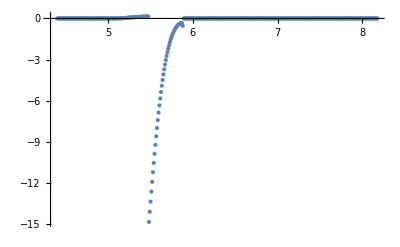

```mathematica
ListPlot[nxhotIm[2],PlotRange->All]
```

## Plot Profiles

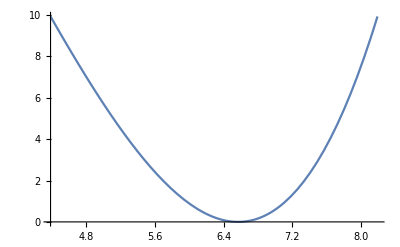

```mathematica
Plot[ψ[x,0.,rMaj,b0,ι0,κ],{x,xmin,xmax}]
```

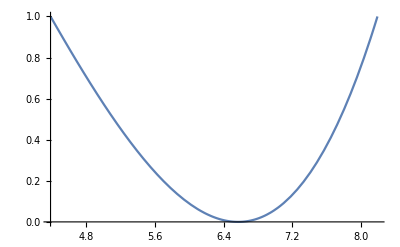

```mathematica
Plot[ψN[x,0.,rMaj,rOut,b0,ι0,κ],{x,xmin,xmax}]
```

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

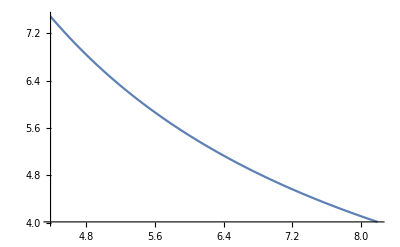

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

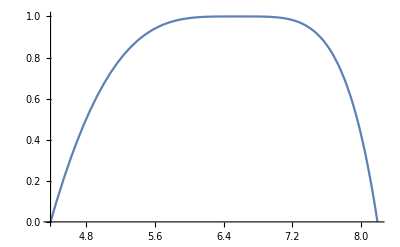

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

```mathematica
αHcut[BXmax,freq, nz,1]
```

0.75 (1+0.0000164662 BXmax)

## Initialization

#### Magnetic field,Density and Temperature Profiles

```mathematica
ψ0[b0_, ι0_]:=b0 ι0/2.
ψ[r_,z_,rMaj_,b0_,ι0_,κ_]:=ψ0[b0, ι0](r^2/rMaj^2 z^2/κ^2+((r^2-rMaj^2)^2)/(4 rMaj^2))
ψB[rMaj_,rOut_,b0_,ι0_,κ_]:=ψ[rOut,0.,rMaj,b0,ι0,κ]
ψN[r_,z_,rMaj_,rOut_,b0_,ι0_,κ_]:=ψ[r,z,rMaj,b0,ι0,κ]/ψB[rMaj,rOut,b0,ι0,κ]
```

```mathematica
bprof[x_]:=b0 rMaj/x
```

```mathematica
nprof[x_]:=If[ψN[x,0.,rMaj,rOut,b0,ι0,κ]<1.,n0(1-ψN[x,0.,rMaj,rOut,b0,ι0,κ]^α2)^α1,0.]
```

```mathematica
tprof[x_]:=If[ψN[x,0.,rMaj,rOut,b0,ι0,κ]<1.,t0(1-ψN[x,0.,rMaj,rOut,b0,ι0,κ]^αT2)^αT1,0.]
```

```mathematica
αHcut[B_,freq_, nz_,sgn_]:=(1-nz^2)×(1+sgn*2.79926 B/freq)
```